```mathematica
(*raw = Import["~/Downloads/optimizerHistory_200um_0.30Best_noRF.json"];
(*raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"];*)*)

RadioButtonBar[
Dynamic[fileName],
{
"~/Downloads/optimizerHistory.json",
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| ~/Downloads/optimizerHistory.json
 | /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]
```

1037

1037

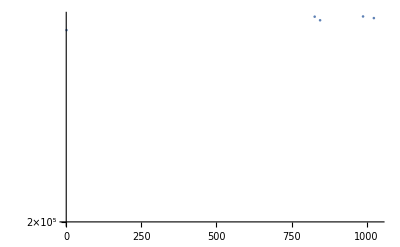

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{2*^5,All},
Joined->False
]
```

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]]
```

<|S1EL_xOffset→-0.000309742,S1EL_yOffset→0.0000861603,S2EL_xOffset→-0.0000342271,S2EL_yOffset→-0.00016854,S2ER_xOffset→-0.000105757,S2ER_yOffset→-0.000714868,S1ER_xOffset→-0.000274391,S1ER_yOffset→-0.000696829,Q5FFkG→-74.867,Q4FFkG→-87.6397,Q3FFkG→107.016,Q2FFkG→120.193,Q1FFkG→-228.412,Q0FFkG→132.091,XC1FFkG→0.244392,XC3FFkG→-0.132678,YC1FFkG→0.00154654,YC2FFkG→0.00244404,PDrive_mean_x→2.5403×10^-6,PDrive_mean_y→7.223×10^-7,PDrive_sigma_x→0.0000606277,PDrive_sigma_y→0.0000151782,PDrive_mean_xp→0.000526345,PDrive_mean_yp→-1.1795×10^-6,PDrive_sigmaSI90_x→0.0000505536,PDrive_sigmaSI90_y→0.0000136893,PDrive_emitSI90_x→0.0000422835,PDrive_emitSI90_y→9.4582×10^-6,PDrive_zLen→0.0000275255,PDrive_zCentroid→991.332,PWitness_mean_x→2.8312×10^-6,PWitness_mean_y→4.1758×10^-6,PWitness_sigma_x→0.0000370809,PWitness_sigma_y→9.853×10^-6,PWitness_mean_xp→0.000438418,PWitness_mean_yp→-0.0000266971,PWitness_sigmaSI90_x→0.0000322482,PWitness_sigmaSI90_y→7.0701×10^-6,PWitness_emitSI90_x→0.0000240753,PWitness_emitSI90_y→4.2615×10^-6,PWitness_zLen→0.0000582506,PWitness_zCentroid→991.332,bunchSpacing→0.000130335,transverseCentroidOffset→3.4657×10^-6,lostChargeFraction→0.,maximizeMe→206007.|>

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

S1EL_xOffset : -0.000309742
S1EL_yOffset : 0.0000861603
S2EL_xOffset : -0.0000342271
S2EL_yOffset : -0.0001685396
S2ER_xOffset : -0.0001057566
S2ER_yOffset : -0.0007148681
S1ER_xOffset : -0.0002743914
S1ER_yOffset : -0.0006968288
Q5FFkG : -74.8669635742
Q4FFkG : -87.6396517866
Q3FFkG : 107.0162683636
Q2FFkG : 120.1925711723
Q1FFkG : -228.4121130463
Q0FFkG : 132.0911865477
XC1FFkG : 0.2443920062
XC3FFkG : -0.1326775504
YC1FFkG : 0.0015465379
YC2FFkG : 0.0024440439
PDrive_mean_x : 2.5403e-6
PDrive_mean_y : 7.223e-7
PDrive_sigma_x : 0.0000606277
PDrive_sigma_y : 0.0000151782
PDrive_mean_xp : 0.0005263446
PDrive_mean_yp : -1.1795e-6
PDrive_sigmaSI90_x : 0.0000505536
PDrive_sigmaSI90_y : 0.0000136893
PDrive_emitSI90_x : 0.0000422835
PDrive_emitSI90_y : 9.4582e-6
PDrive_zLen : 0.0000275255
PDrive_zCentroid : 991.3315843733
PWitness_mean_x : 2.8312e-6
PWitness_mean_y : 4.1758e-6
PWitness_sigma_x : 0.0000370809
PWitness_sigma_y : 9.853e-6
PWitness_mean_xp : 0.0004384176
PWitness_mean_yp : -0.0000266971
PWitness_sigmaSI90_x : 0.0000322482
PWitness_sigmaSI90_y : 7.0701e-6
PWitness_emitSI90_x : 0.0000240753
PWitness_emitSI90_y : 4.2615e-6
PWitness_zLen : 0.0000582506
PWitness_zCentroid : 991.3317147083
bunchSpacing : 0.000130335
transverseCentroidOffset : 3.4657e-6
lostChargeFraction : 0.
maximizeMe : 206006.5766114002

```mathematica
Norm[{bestCase["PDrive_mean_x"],bestCase["PDrive_mean_y"]}-{bestCase["PWitness_mean_x"],bestCase["PWitness_mean_y"]}]
```

3.46573×10^-6

## Plot all

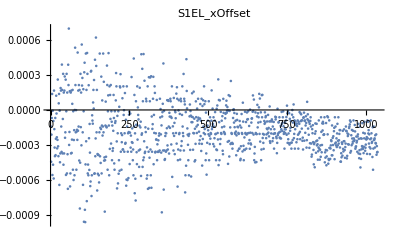
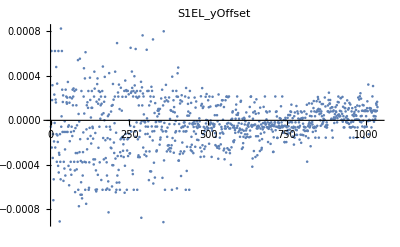
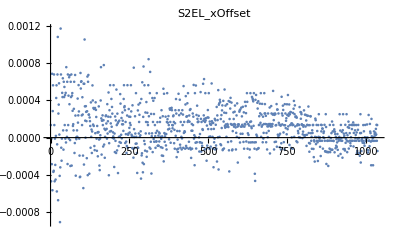
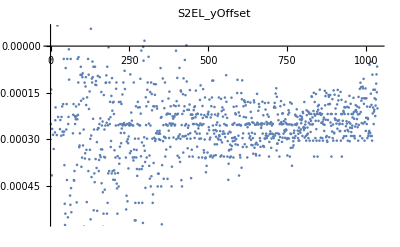
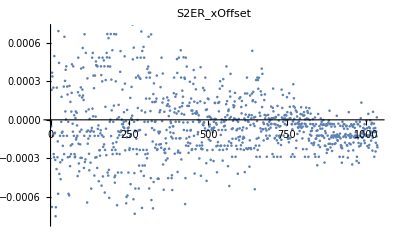
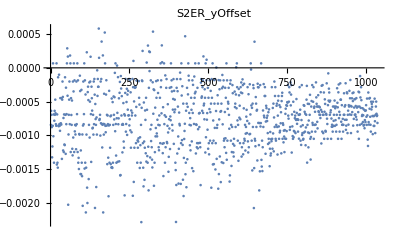
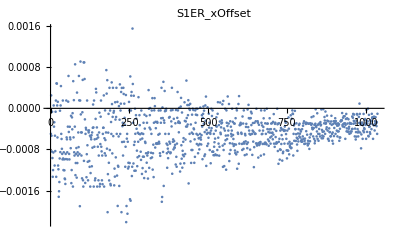
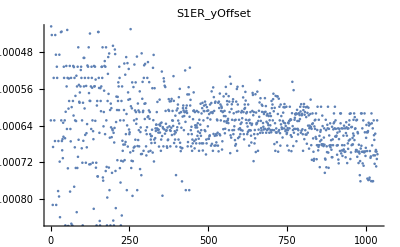
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | 0 | 0

```mathematica
imgArr=Table[
ListPlot[
raw[[All,key]],
PlotLabel->key,
ImageSize->400,
LabelStyle->15
],
{key,Keys[raw[[1]]]}
];

displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"L1PhaseSet","L2PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG", "XC1FFkG","XC3FFkG","YC1FFkG","YC2FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{Q0FFkG,Q1FFkG,Q2FFkG,Q3FFkG,Q4FFkG,Q5FFkG,S1EL_xOffset,S1EL_yOffset,S1ER_xOffset,S1ER_yOffset,S2EL_xOffset,S2EL_yOffset,S2ER_xOffset,S2ER_yOffset,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG}

```mathematica
fitVar = "PDrive_zLen"
```

PDrive_zLen

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

FittedModel[…]

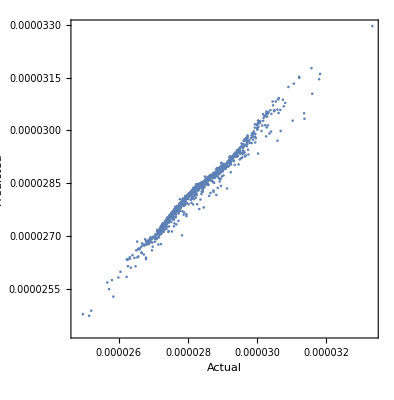

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

```mathematica
Minimize[
lm["BestFit"],
Symbol[#]&/@freeVarsMathematica
]
```

NMinimize::ubnd: The problem is unbounded.

{-∞,{Q0FFkG→Indeterminate,Q1FFkG→Indeterminate,Q2FFkG→Indeterminate,Q3FFkG→Indeterminate,Q4FFkG→Indeterminate,Q5FFkG→Indeterminate,S1ELxOffset→Indeterminate,S1ELyOffset→Indeterminate,S1ERxOffset→Indeterminate,S1ERyOffset→Indeterminate,S2ELxOffset→Indeterminate,S2ELyOffset→Indeterminate,S2ERxOffset→Indeterminate,S2ERyOffset→Indeterminate,XC1FFkG→Indeterminate,XC3FFkG→Indeterminate,YC1FFkG→Indeterminate,YC2FFkG→Indeterminate}}

*facepalm* It’s a linear model, obviously it’s unbounded

```mathematica
lm["ANOVATable"]
```

General::munfl: Exp[-845.818] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1433.01] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1333.02] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| DF | SS | MS | F-Statistic | P-Value
Q0FFkG | 1 | 6.96644×10^-11 | 6.96644×10^-11 | 2767. | 1.49331×10^-292
Q1FFkG | 1 | 1.27227×10^-12 | 1.27227×10^-12 | 50.5332 | 2.20232×10^-12
Q2FFkG | 1 | 3.05821×10^-11 | 3.05821×10^-11 | 1214.69 | 8.31502×10^-176
Q3FFkG | 1 | 2.46652×10^-11 | 2.46652×10^-11 | 979.673 | 3.38005×10^-151
Q4FFkG | 1 | 2.11321×10^-11 | 2.11321×10^-11 | 839.344 | 4.43937×10^-135
Q5FFkG | 1 | 7.37996×10^-12 | 7.37996×10^-12 | 293.124 | 6.09163×10^-58
S1ELxOffset | 1 | 3.17466×10^-11 | 3.17466×10^-11 | 1260.94 | 2.41978×10^-180
S1ELyOffset | 1 | 6.58803×10^-12 | 6.58803×10^-12 | 261.669 | 1.48545×10^-52
S1ERxOffset | 1 | 1.08452×10^-10 | 1.08452×10^-10 | 4307.6 | 0.
S1ERyOffset | 1 | 1.18205×10^-13 | 1.18205×10^-13 | 4.69496 | 0.0304827
S2ELxOffset | 1 | 3.99301×10^-10 | 3.99301×10^-10 | 15859.8 | 0.
S2ELyOffset | 1 | 3.91749×10^-12 | 3.91749×10^-12 | 155.598 | 2.46698×10^-33
S2ERxOffset | 1 | 3.23521×10^-10 | 3.23521×10^-10 | 12849.9 | 0.
S2ERyOffset | 1 | 1.36707×10^-14 | 1.36707×10^-14 | 0.542984 | 0.461368
XC1FFkG | 1 | 1.56911×10^-15 | 1.56911×10^-15 | 0.0623233 | 0.802911
XC3FFkG | 1 | 2.24278×10^-14 | 2.24278×10^-14 | 0.890809 | 0.345482
YC1FFkG | 1 | 9.70464×10^-15 | 9.70464×10^-15 | 0.385458 | 0.534836
YC2FFkG | 1 | 6.45969×10^-13 | 6.45969×10^-13 | 25.6572 | 4.83945×10^-7
Error | 1018 | 2.56301×10^-11 | 2.51769×10^-14 |  | 
Total | 1036 | 1.05466×10^-9 |  |  |

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Plot::plld: Endpoints for x in {x,0.,0.} must have distinct machine-precision numerical values.

Show::gcomb: Could not combine the graphics objects in Show[,Plot[x,{x,Min[lm[Response]],Max[lm[Response]]},PlotStyle→Red]].

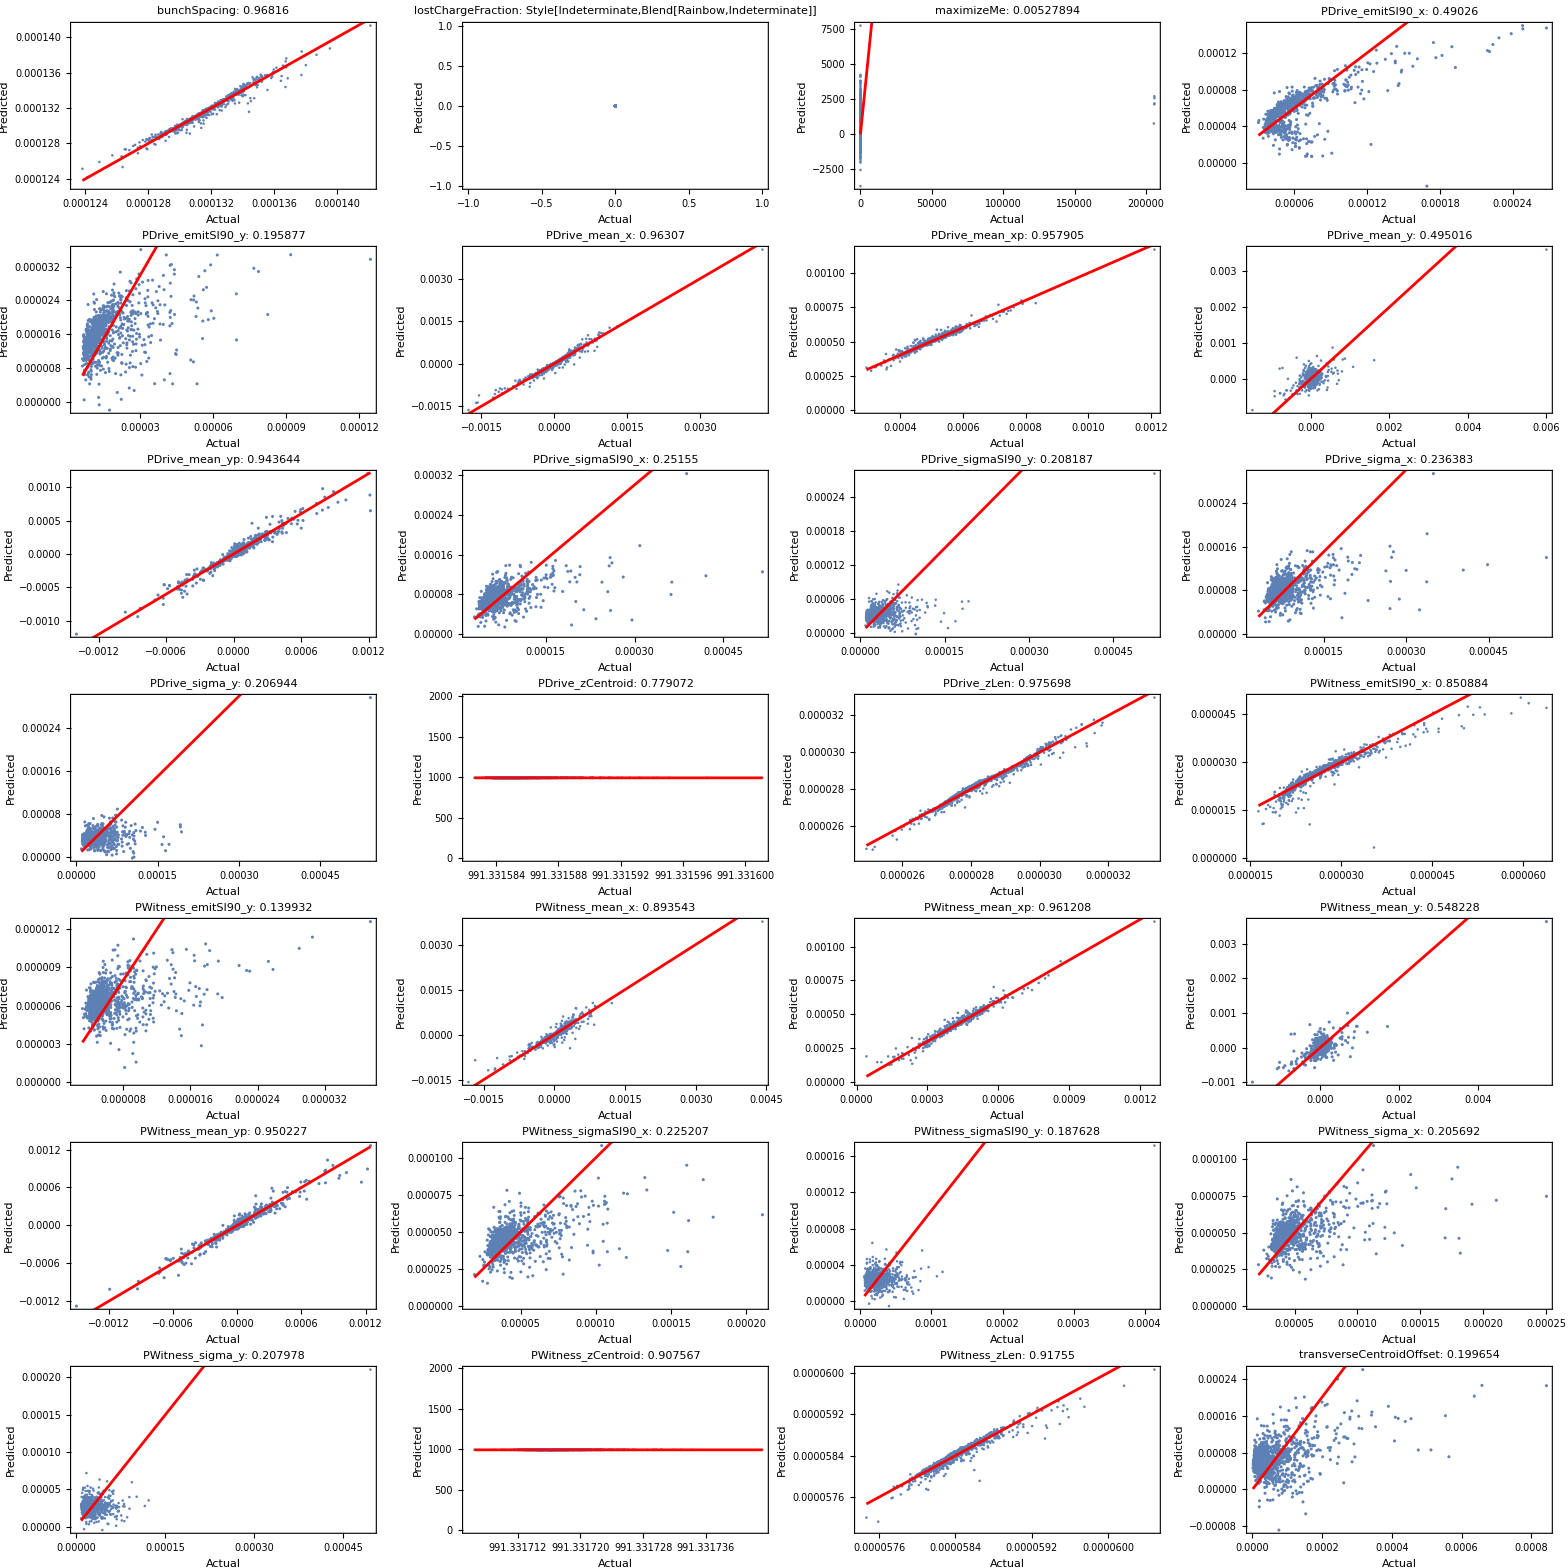

```mathematica
displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```